```mathematica
pca
```

# Principal Components Analysis

## Mean and Variance

### One dimensional problem

Definition of mean and variance:
μ=1/n∑x_i
σ^2=1/n∑(x_i-μ)^2 or sometimes to be unbiased we set n-1 as denominator: σ^2=1/(n-1)∑(x_i-μ)^2

Assuming we have mean μ_(n-1) for some dataset D_(n-1) with n-1 samples.
What would be the mean μ_nif we add a new element x_* to the dataset?
μ_(n-1)=1/(n-1)∑^(n-1) x_i
μ_n=1/n∑^n x_i=1/n(∑^(n-1) x_i+x_*)=1/n((n-1)μ_(n-1)+x_*)=μ_(n-1)+1/n(x_*-μ_(n-1))

Assuming we have mean μ_(n-1) and variance (σ_(n-1))^2 for some dataset D_(n-1) with n-1 samples.
What would be the variance σ_n^2if we add a new element x_* to the dataset (assuming we’ve computed μ_n)?
Recall that μ_n=μ_(n-1)+1/n(x_*-μ_(n-1)) and hence μ_(n-1)=1/(n-1)(nμ_n-x_*) and x_*=nμ_n-(n-1)μ_(n-1)
(σ_(n-1))^2=1/(n-1)∑(x_i-μ_(n-1))^2
σ_n^2=1/n∑(x_i-μ_n)^2
=1/n∑(x_i^2-2 x_i μ_n+μ_n^2)
=1/n∑(x_i^2-2x_i(μ_(n-1)+1/n(x_*-μ_(n-1)))+μ_n^2)
=1/n∑(x_i^2-2 x_i μ_(n-1)+(μ_(n-1))^2-(μ_(n-1))^2-2/n x_i(x_*-μ_(n-1))+μ_n^2)
=1/n∑((x_i-μ_(n-1))^2-(μ_(n-1))^2-2/n x_i(x_*-μ_(n-1))+μ_n^2)
=1/n(∑^(n-1) (x_i-μ_(n-1))^2+(x_*-μ_(n-1))^2+∑(-(μ_(n-1))^2-2/n x_i(x_*-μ_(n-1))+μ_n^2))
=1/n((n-1)(σ_(n-1))^2+(x_*-μ_(n-1))^2+∑(-(μ_(n-1))^2+μ_n^2)-2/n(x_*-μ_(n-1))∑x_i)
=1/n((n-1)(σ_(n-1))^2+(x_*-μ_(n-1))^2-(nμ_(n-1))^2+nμ_n^2-2(x_*-μ_(n-1))μ_n)
=1/n((n-1)(σ_(n-1))^2+(x_*)^2-2 x_*μ_(n-1)+(μ_(n-1))^2-(nμ_(n-1))^2+nμ_n^2-2 x_*μ_n+2 μ_n μ_(n-1))
=1/n((n-1)(σ_(n-1))^2+(x_*-μ_(n-1))(x_*-μ_n))+1/n((μ_(n-1))^2-(nμ_(n-1))^2+nμ_n^2-x_*μ_(n-1)-x_*μ_n+μ_n μ_(n-1))
Replace x_* by nμ_n-(n-1)μ_(n-1) we’ll find out the second term zeros out, leaving only the first term:
σ_n^2=(n-1)/n(σ_(n-1))^2+1/n(x_*-μ_(n-1))(x_*-μ_n)

### Two dimensional problem

Variance of each variable is no longer sufficient to describe correlation between two variables, we introduce co-variance. If co-variance of two variables is positive, increasing one increases the other, else vice versa.

Definition of mean, variance and co-variance:
μ_x=1/n∑x_i | μ_y=1/n∑y_i
σ_x^2=1/n∑(x_i-μ_x)^2 | σ_y^2=1/n∑(y_i-μ_y)^2
σ_xy=σ_yx=1/n∑(x_i-μ_x)(y_i-μ_y)
Co-variance Matrix Cov[x,y]=[σ_x^2 | σ_xy
σ_yx | σ_y^2]

### N-dimensional problem

Definition of variance and co-variance matrix:
Given dataset D={x_1,x_2... x_m}, x_i∈R^Nwhere each x_i represents a data point (not variable) with N variables
μ=1/m∑^m x_i, μ∈R^N
σ^2=1/m∑^m (x_i-μ)⊙(x_i-μ), σ^2∈R^N
σ_(j,k)=1/m∑_i^m (x_(j,i)-μ_j)⊙(x_(k,i)-μ_k)
Cov[D]=[σ_1^2 | σ_(1,2) | ... | σ_(1,N)
σ_(2,1) | σ_2^2 | ... | ...
... | ... | ... | ...
σ_(N,1) | ... | ... | σ_N^2]

Co-variance matrix is guaranteed to be positive semi-definite... What does it mean and why?

### Positive Definite and Semidefinite Matrix

Positive definite matrix

WolframAlphaQueryResults

A positive definite matrix A has all its eigenvalues λ_1... λ_n to be positive. Why?
By definition, for any real vector x this is satisfied: x^T A x>0, that said, matrix A transforms vector x to become another vector A x which must have the same direction as the original vector x in order to satisfy their dot product x^T(A x) to be positive; Since x can be any real vector, it can also be A’s eigenvector v; Then again by definition, transformation of eigenvector A v equals its scalar product with eigenvalue λ v; Putting them together, for all eigenvectors of A, if A v has the same direction as v, its equivalence λ v also has the same direction as v, hence all their scales aka eigenvalues λ_1... λ_n must be positive.

Positive semidefinite matrix

WolframAlphaQueryResults

### Practice Quiz on Mean, Variance and Co-variance

Q1. Compute covariance matrix of dataset:
D={[1
2] | [5
4]} where each column vector represent a data point (not a variable vector!)

Solution from scratch:
μ_x_1=1/2(1+5)=3 | μ_x_2=1/2(2+4)=3
σ_x_1^2=1/2((1-3)^2+(5-3)^2)=4 | σ_x_2^2=1/2((2-3)^2+(4-3)^2)=1
σ_(x_1 x_2)=σ_(x_2 x_1)=1/2((1-3)(2-3)+(5-3)(4-3))=2
A1: Cov[D]=[4 | 2
2 | 1]

```mathematica
Covariance[{{1,2},{5,4}}]
```

{{8,4},{4,2}}

It turns out Mathematica does not divide covariance matrix by number of data points... keep that in mind.

Q2. How would covariance matrix change if we multiply each data point by 2?

A2: The covariance matrix would be scaled by 4.

Q3: How would covariance matrix change if we add a bias of... say 2... at each point?

A3: The covariance matrix does not change.

### Effect on Mean and Co-variance by Linear Transformation on Dataset

Shifting a dataset has effect only on mean but not on variance; Scaling has effect on both mean and variance.

Given dataset D if we perform linear transformation A and bias b we’ll get:
Mean[A·D+b]=A·Mean[D]+b
Cov[A·D+b]=A·Cov[D]·A^T

## Vector

### Dot Product, Inner Product

Dot Product: v_1·v_2
Inner Product: <v_1,v_2>=v_1 ᵀ·A·v_2 (if A is identity matrix I then inner product returns dot product)
Inner Product has the following properties:

#### 1. Symmetry aka Commutativity

<v_1,v_2> =<v_2,v_1>

#### 2. Positive Definiteness

<v_1,v_2>≥0 for all vectors; and <v,v> =0 <->v=0

#### 3. Linearity (aka “Scalar Associativity” + “Distributivity”)

v_1,v_2,v_3∈V, λ∈R
<λ·v_1,v_2> = λ·<v_1,v_2> and <v_1+v_2,v_3> = <v_1,v_3>+<v_2,v_3>
Similarly, we can state it is bilinear, as inner product also satisfies the following:
<v_1,λ·v_2> = λ·<v_1,v_2> and <v_1,v_2+v_3> = <v_1,v_2>+<v_1,v_3>
However, symmetry + linearity already guarantees it is bilinear, hence we don’t have to state it again.

#### Inner Product preserves operations of Dot Product

Length of a vector: ||v||=√<v,v>
Distance between two vectors: ||v_1-v_2||=√<v_1-v_2,v_1-v_2>
Angle’s cosine between two vectors: cos(θ)=(<v_1,v_2>)/(√<v_1,v_1> √<v_2,v_2>)
Scalar projection: ScalarProject(v_1→v_2)=(<v_1,v_2>)/(√<v_2,v_2>)
Vector projection: VectorProject(v_1→v_2)=(ScalarProject(v_1→v_2))/(||v_2||)v_2=(<v_1,v_2>)/(<v_2,v_2>)v_2

### Practice:

```mathematica
Norm[{1,-1,3}]
```

√11

```mathematica
x={3,4};
y={1,-1};
N[VectorAngle[x,y]]
```

1.71269

```mathematica
x={1,2,3};
y={-1,0,8};
N[Norm[x-y]]
N[VectorAngle[x,x-y]]
```

5.74456

2.00283

```mathematica
A={{2,1},{-1,1}};
N[Eigenvalues[A]]
PositiveDefiniteMatrixQ[A]
Plot3D[{Subscript[x, 1],Subscript[x, 2]}.A.{Subscript[x, 1],Subscript[x, 2]},{Subscript[x, 1],-1,1},{Subscript[x, 2],-1,1}]
x={3,4};
y={1,-1};
z={-5,2};
λ=3;
x.A.y==y.A.x
(λ x+y).A.z==λ x.A.z+y.A.z
```

{1.5+0.866025 ⅈ,1.5-0.866025 ⅈ}

True

-Graphics3D-

False

True

```mathematica
Clear[x,y,z,A]
```

```mathematica
InnerProd[x_,A_,y_]:=x.A.y
AngleInnerProd[x_,A_,y_]:=N[ArcCos[InnerProd[x,A,y]/(√InnerProd[x,A,x] √InnerProd[y,A,y])] 180/Pi]
```

```mathematica
x={1,1};y={-1,1};A={{2,-1},{-1,4}};
AngleInnerProd[x,A,y]
```

69.2952

```mathematica
x={0,-1};y={1,1};A={{1,-1/2},{-1/2,5}};
AngleInnerProd[x,A,y]
```

154.158

```mathematica
x={2,2};y={-2,-2};A={{2,1},{1,4}};
AngleInnerProd[x,A,y]
```

180.

```mathematica
x={1,1};y={1,-1};A={{1,0},{0,5}};
AngleInnerProd[x,A,y]
```

131.81

```mathematica
x={1,1,1};y={2,-1,0};A={{1,0,0},{0,2,-1},{0,-1,3}};
AngleInnerProd[x,A,y]
```

78.2218

#### Why Inner Product? → [1] Orthonormal Basis

My guess is we can construct orthonormal basis from the perspective of inner product.
Let’s say a 3-D basis is already orthonormal, then we can represent any vector v by dot product expression:
v=(v·e_1)e_1+(v·e_2)e_2+(v·e_3)e_3 where (v·e_i) is the scalar projection of v on ith basis.
What if the basis a no longer orthonormal? Can we assume they are, from inner product’s perspective?
v=<v,e_1>e_1+<v,e_2>e_2+<v,e_1>e_3 where <v,e_i> = vᵀ·A·e_i
We can only state the above, if we find matrix A so that:
e_i⊥e_j→<e_i,e_j> = 0 (i≠j) and <e_i,e_j> = 1 (i=j)
Let’s find an example!

```mathematica
Subscript[e, 1]={2,0,0};Subscript[e, 2]={-1,2,0};Subscript[e, 3]={-1,-1,2};
A={
{Subscript[a, 11],Subscript[a, 12],Subscript[a, 13]},
{Subscript[a, 12],Subscript[a, 22],Subscript[a, 23]},
{Subscript[a, 13],Subscript[a, 23],Subscript[a, 33]}
};
```

```mathematica
Association[
Solve[Subscript[e, 1].A.Subscript[e, 2]==0&&Subscript[e, 1].A.Subscript[e, 3]==0&&Subscript[e, 2].A.Subscript[e, 3]==0&&Subscript[e, 1].A.Subscript[e, 1]==1&&Subscript[e, 2].A.Subscript[e, 2]==1&&Subscript[e, 3].A.Subscript[e, 3]==1,
{Subscript[a, 11],Subscript[a, 22],Subscript[a, 33],Subscript[a, 12],Subscript[a, 13],Subscript[a, 23]}]
[[1]]];
```

```mathematica
A={
{%[Subscript[a, 11]],%[Subscript[a, 12]],%[Subscript[a, 13]]},
{%[Subscript[a, 12]],%[Subscript[a, 22]],%[Subscript[a, 23]]},
{%[Subscript[a, 13]],%[Subscript[a, 23]],%[Subscript[a, 33]]}
}
```

{{1/4,1/8,3/16},{1/8,5/16,7/32},{3/16,7/32,29/64}}

```mathematica
InnerProd[v_,w_]:=v.A.w
v={-1,5,-4};
v=={InnerProd[v,Subscript[e, 1]],InnerProd[v,Subscript[e, 2]],InnerProd[v,Subscript[e, 3]]}.{Subscript[e, 1],Subscript[e, 2],Subscript[e, 3]}
```

True

```mathematica
PlotVectorProj3D[v_,e1_,e2_,e3_]:=
Show[
Graphics3D[{Red,Arrow[Tube[{{0,0,0},v}]]}],
Graphics3D[Arrow[Tube[{{0,0,0},InnerProd[v,e1] e1}]]],
Graphics3D[Arrow[Tube[{{0,0,0},InnerProd[v,e2] e2}]]],
Graphics3D[Arrow[Tube[{{0,0,0},InnerProd[v,e3] e3}]]],
PlotRange->
{{Min[0,-2,e1[[1]],e2[[1]],e3[[1]]]-1,Max[0,2,e1[[1]],e2[[1]],e3[[1]]]+1},
{Min[0,-2,e1[[2]],e2[[2]],e3[[2]]]-1,Max[0,2,e1[[2]],e2[[2]],e3[[2]]]+1},
{Min[0,-2,e1[[3]],e2[[3]],e3[[3]]]-1,Max[0,2,e1[[3]],e2[[3]],e3[[3]]]+1}}
]
Manipulate[PlotVectorProj3D[{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3]},Subscript[e, 1],Subscript[e, 2],Subscript[e, 3]],
{Subscript[v, 1],-2,2},{Subscript[v, 2],-2,2},{Subscript[v, 3],-2,2}]
```

If we manipulate vector v above, we observe this vector and its projection on basis form a parallelopiped.

This proves that I’m able to find the desired inner product given at least one particular basis.
So generally, does this method always guarantee to find unique solution to define inner product?...

#### Why Inner Product? → [2] Concept Generalization → [2.1] Random Variables

We can view random variables from perspective of inner product.
Say we have two variables x and y in a dataset, we define covariance as their inner product:
<x,y> = σ_(x,y)
What does it mean?... let’s explore the geometric angle of these two “vectors”...
Recall how we define angle’s cosine of inner product: cos(θ)=(<x,y>)/(√(<x,x> <y,y>))

Case 1: x and y are orthogonal “vectors” → we would expect cos(θ)=0
cos(θ)=(σ_(x,y))/(σ_x σ_y)=0 → σ_(x,y)=0
The way to interpret it, is to say x and y are two uncorrelated variables.

Case 2: x and y are parallel “vectors” pointing to same direction → we would expect cos(θ)=1
cos(θ)=(σ_(x,y))/(σ_x σ_y)=1 → σ_(x,y)=σ_x σ_y>0
If we standardize these two variables x and y beforehand, we would expect σ_(x,y)=1
That is to say x and y are positively correlated, but not necessarily saying x and y are the same variables.

Case 3: x and y are parallel “vectors” pointing to opposite directions → we’d expect cos(θ)=-1
Similarly we’d get σ_(x,y)=-σ_x σ_y<0 and if we standardize both beforehand, we’d expect σ_(x,y)=-1
That is to say x and y are negatively correlated, but again not necessarily saying x=-y.

#### Why Inner Product? → [2] Concept Generalization → [2.2] Functions

So far we have viewed inner product as a discrete operation... what if we apply it to continuous objects?
Say there are two functions f(x) and g(x) both of which are continuous:
f(x)=sin(x), g(x)=cos(x)
Recall that inner product of two vectors are the sum of their multiplied elements: <v_1,v_2> = v_1 ᵀ·A·v_2
Then inner product of two functions must be the integral of their multiplication: < f, g > = ∫_a^b f(x)g(x)dx
Hence, <sin(x),cos(x)> = ∫_a^b sin(x)cos(x)dx

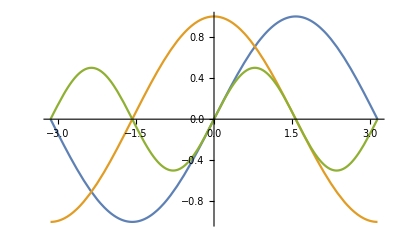

```mathematica
Plot[{Sin[x],Cos[x],Sin[x]Cos[x]},{x,-Pi,Pi}]
```

```mathematica
ProdFG[x_]:=Sin[x] Cos[x]
ProdFG[-π]==-ProdFG[π]
```

True

So the product of sin(x) and cos(x), which is sin(x)cos(x) is an odd function. What does it tell us?
This tells us that sin(x) and cos(x) are orthogonal from -x to +x where x∈ℝ

Shall we verify this fact using inner product’s angle concept?
Recall that angle’s cosine between two vectors are: cos(θ)=(<v_1,v_2>)/(√<v_1,v_1> √<v_2,v_2>)
The angle’s cosine between two functions are: cos(θ)=(∫f(x)g(x)dx)/(√∫(f(x))^2 dx √∫(g(x))^2 dx)
To verify the two functions are orthogonal in a given range, we need their cosine to be zero, which means:
• Their inner product in that range evaluates to zero
• Their norms in that range (root of inner product to themselves respectively) evaluates to non-zero

```mathematica
InnerProdFG[a_,b_]:=Evaluate[∫_a^b Sin[x]Cos[x]ⅆx]
NormF[a_,b_]:=Evaluate[√∫_a^b Sin[x]^2 ⅆx]
NormG[a_,b_]:=Evaluate[√∫_a^b Cos[x]^2 ⅆx]
AngleFG[a_,b_]:=ArcCos[InnerProdFG[a,b]/(NormF[a,b] NormG[a,b])] 180/π
AngleFG[-π,π]°
```

90 °

This proves our observation!

## Orthogonal Projection

Say we want to project vector x onto subspace B using a linear combination λ:
x=[x_1
...
x_D], x∈ℝ^D		B=[b_1... b_M], B∈ℝ^(D×M)		λ=[λ_1
...
λ_M], λ∈ℝ^M
This projection Π_B(x) must have the following key properties:
(1) Π_B(x)=∑_i^M λ_i b_i=B λ, Π_B(x)∈ℝ^D
(2) <Π_B(x)-x,b_i> = 0, i=1...M ⟷ <Π_B(x)-x,B> = 𝟘^(1×M)
Substitute (1) into (2): <B λ,B>-<x,B> = 𝟘^(1×M)
If we select dot product as inner product: (B λ)ᵀB-xᵀB=λᵀBᵀB-xᵀB=𝟘
And solve the equation above: λ=(xᵀB·(BᵀB)^-1)ᵀ=((BᵀB)^-1)ᵀ·(xᵀB)ᵀ=(BᵀB)^-1 Bᵀx
Substitute λ above into (1): Π_B(x)=B λ=B (BᵀB)^-1 Bᵀx
Note that the formula above excluding x is called projection matrix: B (BᵀB)^-1 Bᵀ

Properties of projection matrix:
• Pᵀ=P, proof: Pᵀ=(B (BᵀB)^-1 Bᵀ)ᵀ=B((B(BᵀB))^-1)ᵀ=B((BᵀB)^-1)ᵀBᵀ=B (BᵀB)^-1 Bᵀ=P
• PᵀP=P, proof: PᵀP=P P=B (BᵀB)^-1 Bᵀ·B (BᵀB)^-1 Bᵀ=B (BᵀB)^-1((BᵀB)(BᵀB)^-1)Bᵀ=B (BᵀB)^-1 Bᵀ=P

Special cases:
• If B is orthonormal basis: BᵀB=𝕀^(D×D) → Π_B(x)=B Bᵀx
• If B is just a 1D subspace which can be written as b, then: λ=bᵀx/bᵀb, Π_b(x)=(b bᵀ)/bᵀb x

## Multivariate Calculus

### Chain rules

f(x)=f(x_1,x_2,...,x_n)
x(t)=[x_1(t)
x_2(t)
...
x_n(t)]
∂_t f(t)=∂_x f(x)·∂_t x(t)=J_f·∂_t x(t)

Practice on 2-step chain rule:

```mathematica
u[t_]:=t^2
x[t_]:=1-u[t]
f[t_]:=5 x[t]
```

```mathematica
f[t]
f'[t]
```

5 (1-t^2)

-10 t

### Lagrangian Multiplier

Lagrange multiplier

WolframAlphaQueryResults

2D example of Lagrange multiplier:
Find maxima/minima of a function f(x,y) with constraint g(x,y)=0

```mathematica
f[x_,y_]:=-ⅇ^(x-y^2+x y)
g[x_,y_]:=Cosh[y]+x-2
Lagrange[x_,y_,λ_]:=f[x,y]+λ g[x,y]
```

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

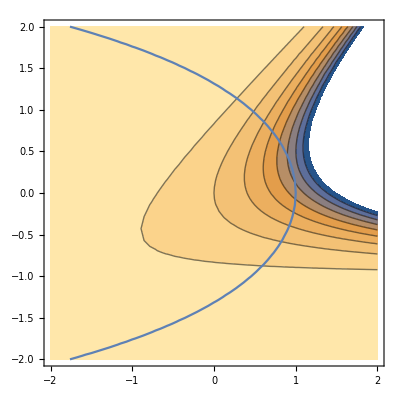

```mathematica
Show[
ContourPlot[f[x,y],{x,-2,2},{y,-2,2}],
ContourPlot[g[x,y]==0,{x,-2,2},{y,-2,2}]
]
```

From our observation on contour plot above, we can already point out the extrema given constraint.
We just need to program it and let computer do the job.

```mathematica
Subscript[y, 0]=0;Subscript[x, 0]=Association[Solve[g[x,Subscript[y, 0]]==0,x]][x];Subscript[λ, 0]=1;
```

```mathematica
xyλ=Association[FindRoot[{D[Lagrange[x,y,λ], x],D[Lagrange[x,y,λ], y],g[x,y]},
{{x,Subscript[x, 0]},{y,Subscript[y, 0]},{λ,Subscript[λ, 0]}}]];
```

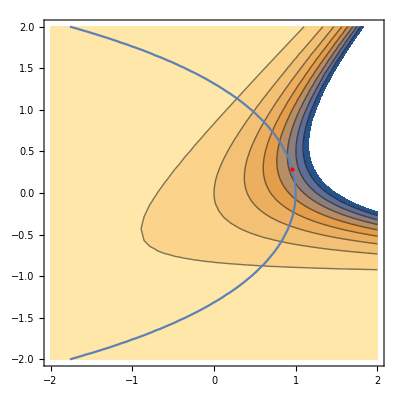

```mathematica
Show[%33,Graphics[{Red,PointSize[Large],Point[{xyλ[x],xyλ[y]}]}]]
```

## PCA

Before we move on to PCA, a couple of terminologies need to be defined:
• Vector space
• Orthogonal decomposition
• Orthogonal complement

Vector space

WolframAlphaQueryResults

Orthogonal complement

WolframAlphaQueryResults

Orthogonal decomposition

WolframAlphaQueryResults

### PCA derivation

Stating the problem:
Given a dataset: X={x_1,...,x_N}, x_n∈ℝ^D
Find optimal basis: B={b_1,...,b_M}
in order to project: (x̃)_n=B Bᵀ x_n, where Bᵀ x_n is the coordinates / codes of x_n projected onto B
(A) x_n=∑_i^D β_(i,n)b_i, using orthogonal decomposition: (x̃)_n=∑_(i=1)^M β_(i,n)b_i, hence: x_n=(x̃)_n+∑_(i=M+1)^D β_(i,n)b_i

Assume:
• Centered data: E[x]=0
• Orthonormal basis (ONB): b_i ᵀ b_j=0 if i≠j else 1

Objective: Minimize mean square error
(B) J=1/N∑_n^N||x_n-(x̃)_n(||)^2

Our approach: Set partial derivatives of J w.r.t. parameters β_(i,n) and b_i to zero.
(C) ∂_((x̃)_n) J=-2/N(x_n-(x̃)_n)ᵀ
∂_{β_(i,n),b_i} (x̃)_n={b_i,β_(i,n)}
∂_(β_(i,n)) J=∂_((x̃)_n) J·∂_(β_(i,n)) (x̃)_n=-2/N(x_n-∑_j^M β_(j,n)b_j)ᵀ b_i=^ONB-2/N(x_n ᵀ b_i-β_(i,n))
∂_(β_(i,n)) J=0  ⟷  (D) β_(i,n)=x_n ᵀ b_i=b_i ᵀ x_n
This means, the optimal coordinates β_(i,n) is the coordinates of orthogonal projection of data (x̃)_n onto basis b_i.
(x̃)_n=^(A)∑_(i=1)^M β_(i,n)b_i=^(D)∑_(i=1)^M (b_i ᵀ x_n)b_i  ⟷  (E) x_n-(x̃)_n=∑_(i=M+1)^D (b_i ᵀ x_n)b_i
J=^(B)1/N∑_n^N||x_n-(x̃)_n(||)^2=^(E)1/N∑_n^N||∑_(i=M+1)^D (b_i ᵀ x_n)b_i(||)^2=^ONB 1/N∑_n^N ∑_(i=M+1)^D (b_i ᵀ x_n)^2=1/N∑_n^N ∑_(i=M+1)^D b_i ᵀ x_n x_n ᵀ b_i=∑_(i=M+1)^D b_i ᵀ(1/N∑_n^N x_n x_n ᵀ)b_i
If we look carefully at the middle term 1/N∑_n^N x_n x_n ᵀ, it happens to be Covariance Matrix S, let’s rewrite it:
(F) J=∑_(i=M+1)^D b_i ᵀS b_i=(∑_(i=M+1)^D b_i b_i ᵀ)S
We can also interpret ∑_(i=M+1)^D b_i b_i ᵀ as projection matrix, which projects data covariance matrix S onto the orthogonal complement of our principal subspace. In other words, minimizing loss function J is equivalent to minimizing the original data’s projection onto the subspace that we ignore in PCA.
To minimize loss function J with ONB constraints: b_i ᵀ b_i=1, we use Lagrange Multiplier approach:
L=J+∑_(i=M+1)^D λ_i(1-b_i ᵀ b_i)=^(F)∑_(i=M+1)^D (b_i ᵀS b_i+λ_i(1-b_i ᵀ b_i))
∂_b_i L=2b_i ᵀS-2 λ_i b_i ᵀ
∂_b_i L=0  ⟷  (G) S b_i=λ_i b_i, this turns to a problem of finding eigenvalues λ of covariance matrix S
J=^(F)∑_(i=M+1)^D b_i ᵀS b_i=^(G)∑_(i=M+1)^D b_i ᵀ b_i λ_i=^ONB∑_(i=M+1)^D λ_i
Minimize J  ⟷  Minimize ∑_(i=M+1)^D λ_i  ⟷  Maximize ∑_(i=1)^M λ_i
Therefore, choosing eigenvectors with the largest eigenvalues for our principal subspace will help us achieve our goal of retaining maximum variance.

### PCA algorithms step-by-step

#### 1. Center the data

• x_n=x_n-μ, where μ∈ℝ^D (not necessary but good practice to make computation easy)
• x_n=x_n/σ, where σ∈ℝ^D (not necessary for data with same unit esp. unstructured data e.g. images)

#### 2. Compute covariance matrix S

S=1/N∑_n^N x_n x_n ᵀ, where x_n∈ℝ^D

#### 3. Find eigenvalues and eigenvectors of S

S b_i=λ_i b_i

#### 4. Choose eigenvectors with top-M eigenvalues as principal components

B=argmax_{b_1,...,b_M}∑_(i=1)^M λ_i, where B∈ℝ^(D×M)

#### 5. Reconstruct any data x_n by projecting it onto principal subspace

(x̃)_n=B Bᵀ x_n, to reiterate: the term Bᵀ x_n is the coordinates / codes of x_n projected onto B
Some unstructured data may be recoverable: (x̃)_n=σ(x̃)_n+μ, where μ,σ∈ℝ^D

### PCA (alternative) algorithms for high-dimensional data: When N≪D

If dimension is very high, computing covariance matrix of D×D can be extremely expensive. However if we have substantially fewer number of data points N, there is an alternative of PCA to optimize efficiency.
Given a dataset: X={x_1,...,x_N}, x_n∈ℝ^D
Its covariance matrix is: S=1/N X Xᵀ, S∈ℝ^(D×D)
N≪D ⟶ rank(S)=N, that means the covariance matrix is not full ranked, there are D-N+1 eigenvalues that are zero, the rows and columns are linearly dependent, in other words, there are some redundancies.
Now let’s convert the covariance matrix into N×N so that the computation is less expensive.
S b_i=λ_i b_i ⟶ 1/NX Xᵀ b_i=λ_i b_i ⟶ (1/N XᵀX )Xᵀ b_i=λ_i Xᵀ b_i
Let c_i be Xᵀ b_i, we can rewrite our covariance matrix as: S̃=1/N XᵀX, S̃∈ℝ^(N×N), such that: S̃ c_i=λ_i c_i, where c_i is eigenvector of covariance S̃; In this way, we have successfully reduced dimensions of covariance matrix.
One thing to pay attention: We have to normalize eigenvector c_i such that its norm equals 1, otherwise we won’t be able to exploit ONB properties.
To recover the original covariance matrix S and eigenvector b_i, we left multiply the equation by X again: X S̃ c_i=λ_i X c_i ⟶ (1/N X Xᵀ)X c_i=λ_i X c_i ⟶ S (X c_i)=λ_i(X c_i), S∈ℝ^(D×D)

### Other interpretations of PCA

PCA can be viewed from different perspectives:
• Minimizing squared reconstruction error
• Minimizing auto-encoder loss
• Maximizing mutual information
• Maximizing variance of projected data
• Maximizing likelihood in a latent variable model
All these different perspectives give us the same solution to PCA problem.